## Time dependent behaviors

### Time domain parameters

### Time domain behavior for both systems

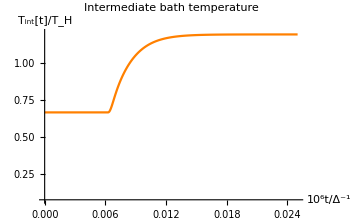
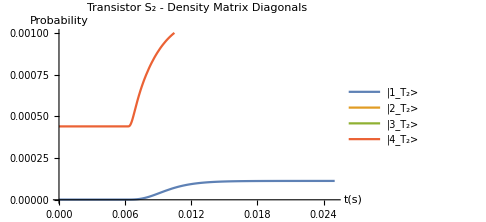
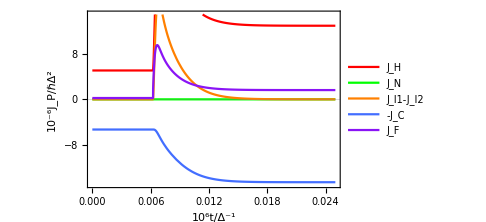
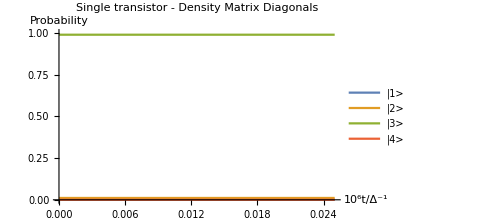
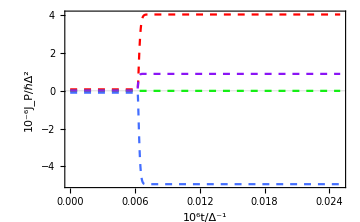
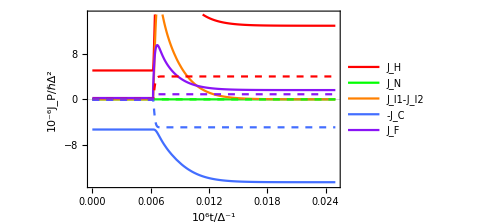

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax},
ωLM1=0.3 ωconv;ωMR1=0.4 ωconv;
ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
mCint=0.4mCconv;
Ωcnt1s=0.0004ωconv;Ωcnt2s=0.003ωconv;
tmax=(100/(ωMR1 κhot));tchange=0.25 tmax;tstart=-10tmax;
PlotTimeDomainWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax]
]
```

```mathematica
PlotTimeDomainWithΩ[Thots_,Tcnts_,Tcols_,κhots_,κcnts_,κints_,κcols_,mCints_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,Ω2_, Ωcnt1s_,Ωcnt2s_,tstart_,tchange_,tmax_]:=Module[{timeassum,sysassum,indsysassum,motioneqs,indmotioneqs,initconditions,indinitconditions,dynamics,inddynamics,tempgraph,denmatS2graph,flowgraph,inddenmatgraph,indflowgraph},
timeassum:={
Ωcnt-> Piecewise[{{Ωcnt1,t<tchange},{Ωcnt2,t>tchange}}],
Ωcnt1->Ωcnt1s,
Ωcnt2->Ωcnt2s
};
sysassum = {
Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,
Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,
Subscript[Ω, 1]->Ωcnt,Subscript[Ω, 2]->Ω2,
Thot-> Thots,Tcol-> Tcols,Tcnt-> Tcnts,
κhot->κhots,κcol->κcols,κcnt->κcnts,κint->κints,
mCint->mCints
};

motioneqs={Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,timeassum,Jassum,NBEassum,Tassum}];
initconditions={Tint[tstart]==Tcols,Table[Subscript[ρ, S,i,j][tstart]==i,j i,3 1,{S,1,2},{i,1,4},{j,1,4}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,4},{j,1,4}],Tint}],{t,tstart,tmax}
];

tempgraph = (Tint[#]/Thot)/.Flatten[{dynamics,sysassum}] &;
denmatS2graph=Flatten[{Table[Subscript[ρ, 2,i,i][10^6 t],{i,1,4}]}/.dynamics];
flowgraph=Flatten[10^6{
Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 1,2],-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2]),Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 1]+Subscript[EngyFlowInField, 2]
}//.Flatten[{unitassum,ωassum,ωassum1,timeassum,sysassum,Jassum,NBEassum,Tassum}]/.dynamics]/.t->10^6 ts;


indsysassum={
Subscript[ωLM, 1]->ωLM2,Subscript[ωMR, 1]->ωMR2,
Subscript[T, 1,1]-> Thots,Subscript[T, 1,2]-> Tcnts,Subscript[T, 1,3]->Tcols,
Subscript[κ, 1,1]-> κhots,Subscript[κ, 1,2]-> κcnts,Subscript[κ, 1,3]->κcols,
Subscript[Ω, 1]->Ωcnt
};

indmotioneqs=Subscript[motioneq, 1]//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,timeassum}];
indinitconditions={Table[Subscript[ρ, 1,i,j][tstart]==i,j i,3 1,{i,1,4},{j,1,4}]}/.indsysassum;

inddynamics = NDSolve[
Flatten[{indmotioneqs,indinitconditions}]
,Flatten[{Table[Subscript[ρ, 1,i,j],{i,1,4},{j,1,4}]}],{t,tstart,tmax}
];

inddenmatgraph=Flatten[{Table[Subscript[ρ, 1,i,i][10^6 t],{i,1,4}]}/.singdynamics];
indflowgraph=Flatten[10^6{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3],Subscript[EngyFlowInField, 1]
}//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,Tassum,timeassum}]/.inddynamics]/.t->10^6 ts;

{{
Plot[tempgraph[10^6 t],{t,0,10^-6 tmax},
ImageSize->Medium,
	PlotLabel->  Style["Intermediate bath temperature"],
	PlotRange-> {(0.8Tcol/Thot)/.sysassum,(1.2Thot/Thot)/.sysassum},
	AxesLabel->{Style["10^6t/Δ^-1"],Style["T_int[t]/T_H"]},
	PlotStyle->{Orange}
],
Plot[denmatS2graph,{t,0,10^-6 tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S_2 - Density Matrix Diagonals"],
	PlotRange-> {0.0,0.001},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}
],
timedom=Plot[flowgraph,{ts,0,10^-6 tmax},
	ImageSize->Medium,
	PlotRange->{Automatic,{-15,15}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->{
		Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5],
		Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]},
	PlotStyle->{{Red},{Green},{Orange},{BlueC},{PurpleC}}
]
},
{
Plot[inddenmatgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Single transistor - Density Matrix Diagonals"],
PlotRange-> {0.0,1},
AxesLabel->{Style["10^6t/Δ^-1"],Style["Probability"]}, 
PlotLegends->{
Style["|1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4>",FontFamily->"Times New Roman",FontSize->14.5]}
],
singtimedom=Plot[indflowgraph,{ts,0,10^-6 tmax},
ImageSize->Medium,
PlotRange->{Automatic,Full},
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
PlotStyle->{{Red,Dashed},{Green,Dashed},{BlueC,Dashed},{PurpleC,Dashed}}]
},
{Show[timedom,singtimedom]}}
]
```

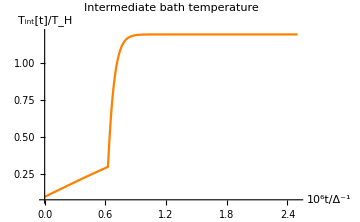
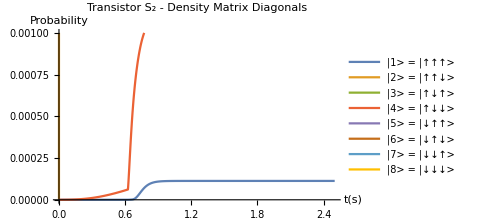
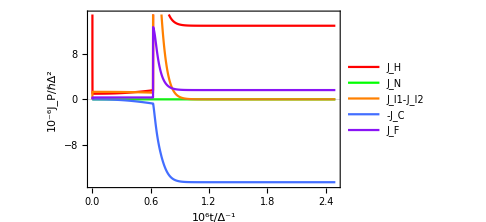

```mathematica
motioneqs={Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,timeassum,Jassum,NBEassum,Tassum}];
initconditions={Tint[tstart]==Tcol,Table[Subscript[ρ, S,i,j][tstart]==i,j i,3 1,{S,1,2},{i,1,4},{j,1,4}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,8},{j,1,8}],Tint}],{t,tstart,tmax}
];

Tints=(Tint[#]/Thot)/.Flatten[{dynamics,sysassum}] &;
diags=Flatten[{Table[Subscript[ρ, 2,i,i][10^6 t],{i,1,8}]}/.dynamics];
combflows=Flatten[10^6{
Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 1,2],-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2]),Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 1]+Subscript[EngyFlowInField, 2]
}//.Flatten[{unitassum,ωassum,ωassum1,timeassum,sysassum,Jassum,NBEassum,Tassum}]/.dynamics]/.t->10^6 ts;


{
Plot[Tints[10^6 t],{t,0,10^-6 tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Intermediate bath temperature"],
	PlotRange-> {(0.8Tcol/Thot)/.sysassum,(1.2Thot/Thot)/.sysassum},
	AxesLabel->{Style["10^6t/Δ^-1"],Style["T_int[t]/T_H"]},
	PlotStyle->{Orange}
],
Plot[diags,{t,0,10^-6 tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S_2 - Density Matrix Diagonals"],
	PlotRange-> {0.0,0.001},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}],
timedom=Plot[combflows,{ts,0,10^-6 tmax},
	ImageSize->Medium,
	PlotRange->{Automatic,{-15,15}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->{
		Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5],
		Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]},
	PlotStyle->{{Red},{Green},{Orange},{BlueC},{PurpleC}}]
}
```

### Single transistor system

Numerical solution of the dynamics, with the initial condition that all density matrix elements except the third are zero (ground/lowest energy state).

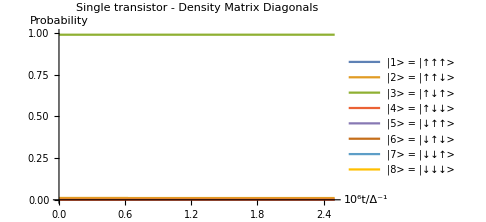

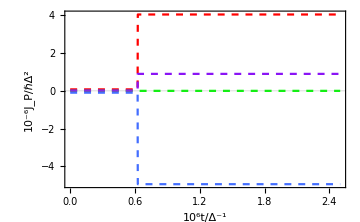

```mathematica
motioneqs=Subscript[motioneq, 1]//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,timeassum}];
initconditions={Table[Subscript[ρ, 1,i,j][tstart]==i,j i,3 1,{i,1,4},{j,1,4}]}/.sysassum;

singdynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, 1,i,j],{i,1,8},{j,1,8}]}],{t,tstart,tmax}
];

Flatten[{Table[Subscript[ρ, 1,i,i][10^6 t],{i,1,8}]}/.singdynamics];
Plot[%,{t,0,10^-6 tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Single transistor - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["10^6t/Δ^-1"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}]

Flatten[10^6{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3],Subscript[EngyFlowInField, 1]
}//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,Tassum,timeassum}]/.singdynamics]/.t->10^6 ts;
singtimedom=Plot[%,{ts,0,10^-6 tmax},
	ImageSize->Medium,
	PlotRange->{Automatic,Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotStyle->{{Red,Dashed},{Green,Dashed},{BlueC,Dashed},{PurpleC,Dashed}}]
```

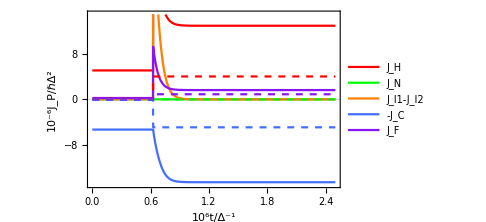

```mathematica
Show[timedom,singtimedom]
```